```mathematica
Show[
Plot[{x Log2[1 + 1/x], Log2[E]}, {x, 0, 10}, PlotTheme->"Detailed", PlotRange->All,  PlotLegends->Placed[{"Capacity", "Infinite Bandwidth limit"},{0.65,0.5}], PlotStyle->(Directive[AbsoluteThickness[4],#]&/@{Hue[0.58,1,1],Hue[0.12,1,1]}), ImageSize->600],AxesOrigin->{0,0}, FrameLabel->{"Bandwidth B [Hz]", "Channel Capacity C [bits/s]"}, LabelStyle->{FontFamily->"Helvetica",14,Black}
]
```

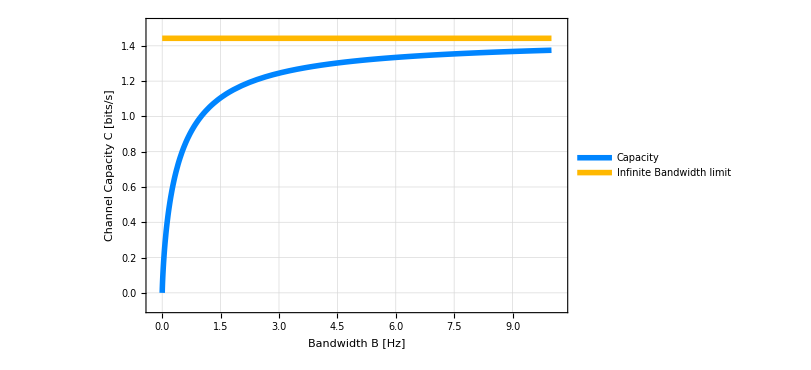

```mathematica
styleoptions=Sequence@@{BaseStyle->Gray,Filling->Axis,Frame->True,FillingStyle->Array[#->Opacity[0.3,{Hue[0.58,1,1],Hue[0.12,1,1],Hue[0,1,1],Hue[0.5,1,.7],Hue[0.67,.5,1],Hue[0.17,1,.8],Hue[0.9,1,.8],Hue[0.11,.7,.9],Hue[0.61,1,1],Hue[0.08,1,1]}[[#]]]&,10],LabelStyle->{FontFamily->"Helvetica",14,Gray},PlotStyle->(Directive[AbsoluteThickness[4],#]&/@{Hue[0.58,1,1],Hue[0.12,1,1],Hue[0,1,1],Hue[0.5,1,.7],Hue[0.67,.5,1],Hue[0.17,1,.8],Hue[0.9,1,.8],Hue[0.11,.7,.9],Hue[0.61,1,1],Hue[0.08,1,1]})};
```

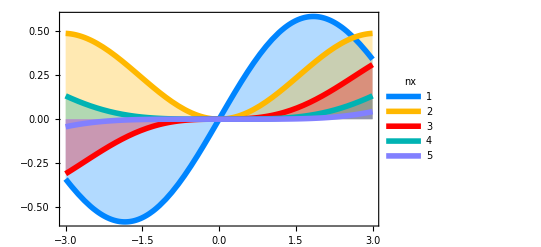

```mathematica
Plot[Evaluate[Table[BesselJ[n,x],{n,1,5,1}]],{x,-3,3},ImageSize->400,PlotLegends->Placed[LineLegend[Range[1,5],LabelStyle->{Gray,Bold,18},LegendLabel->BesselJ[n,x],LegendLayout->{"Row",2}],{0.75,0.25}],Evaluate@styleoptions]
```

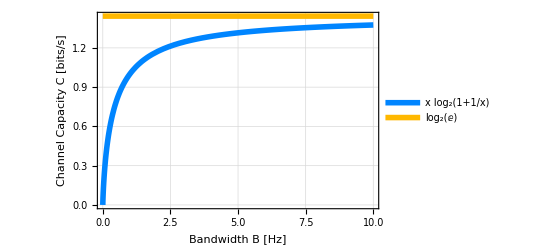

```mathematica
Show[
Plot[{x Log2[1 + 1/x], Log2[E]}, {x, 0, 10}, PlotTheme->"Detailed", PlotRange->All,  PlotStyle->(Directive[AbsoluteThickness[4],#]&/@{Hue[0.58,1,1],Hue[0.12,1,1]})],AxesOrigin->{0,0}, FrameLabel->{"Bandwidth B [Hz]", "Channel Capacity C [bits/s]"}, LabelStyle->{FontFamily->"Helvetica",12,Black}
]
```